MagneticTB 入门

要构造紧束缚模型，需要给出晶格、原子位置、对称操作和局域轨道。有了这些输入，MagneticTB 就可以生成等价原子，求出对称性允许的跃迁。下面以石墨烯为例，介绍如何构造 Hamiltonian 并画出能带。

安装、更新、卸载与加载

安装前需要取得 MagneticTB 的 .paclet 文件，也可以从源码构建。下面使用本地文件安装，不会从网上自动下载。

### 安装

MagneticTB 帮助主页

取得 .paclet 文件后，在 Mathematica 中运行下面的命令，其中路径和文件名要换成实际文件：

```mathematica
PacletInstall["/absolute/path/MagneticTB-2.x.y.paclet"]
```

安装后，请完全退出 Mathematica 再重新打开，然后加载 MagneticTB 或打开帮助文档。这样也可以清除先前版本在内核中留下的定义。

### 更新

MagneticTB 帮助主页

更新时，按同样的方法安装新的 .paclet 文件，再退出并重新打开 Mathematica。如果出现 PacletInstall::samevers，说明相同版本已经安装；要换成同版本的另一个文件，需要先卸载该版本，再重新安装。

```mathematica
PacletInstall["/absolute/path/MagneticTB-2.x.y.paclet"]
```

### 卸载或重装同一版本

MagneticTB 帮助主页

如果不再使用 MagneticTB，可以运行下面的命令卸载，再退出并重新打开 Mathematica：

```mathematica
PacletUninstall["MagneticTB"]
```

### 加载并打开帮助文档

MagneticTB 帮助主页

重新打开 Mathematica 后，使用 Needs 加载程序包。在帮助中心搜索 MagneticTB，或运行下面的命令，都可以打开帮助主页。1.0 版函数使用 MagneticTBOld` 加载，需要与 2.0 版分别在不同内核中使用。

```mathematica
Needs["MagneticTB`"]
```

```mathematica
SystemOpen["paclet:MagneticTB/guide/MagneticTB"]
```

五类物理输入

有了对称操作，就可以使用 init 设置晶格、原子位置和基函数。其中 lattice 的三行分别是三个晶格基矢，lattpar 给出晶格参数；wyckoffposition 给出各个不等价 Wyckoff 位置的代表原子及磁矩；symminformation 是对称操作，basisFunctions 按相同顺序列出各位置的局域轨道。

石墨烯的两个碳原子是对称等价的，只需输入 {1/3,2/3,0}，程序就会生成另一个位置 {2/3,1/3,0}。每个碳原子保留一个 pz 轨道，晶格参数 c 用来分隔周期重复的石墨烯层。

| lattice | 长度 | 按行存储三条原胞基矢。wyckoffposition 中的坐标是相对于该基的分数坐标。
       | lattpar | 长度 | 为每个符号晶格常数给出数值。MagneticTB 不强制使用埃作为单位；所有长度必须采用一致单位。
       | wyckoffposition | 分数坐标与磁矩 | 外层列表枚举不等价 Wyckoff 轨道。每个条目为 {种子位置, 磁矩}；basisFunctions 使用相同的外层顺序。
       | symminformation | 对称操作 | 每条磁群记录都是 {label,R,t,"F"|"T"}；最后一个字段记录该操作是幺正还是反幺正。
       | basisFunctions | 局域轨道基底 | 每条 Wyckoff 轨道对应一个非空局域基列表。不同条目可以具有不同维数，从而产生矩形的轨道间 hopping 分块。

```mathematica
grapheneOperations = msgop[gray[191]];
init[
  lattice -> {
    {a, 0, 0},
    {-a/2, Sqrt[3] a/2, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 3},
  wyckoffposition -> {
    {{1/3, 2/3, 0}, {0, 0, 0}}
  },
  symminformation -> grapheneOperations,
  basisFunctions -> {{"pz"}}
];
```

查看原子坐标和磁化方向

初始化后，输入 atompos 就可以查看生成的原子坐标和磁化方向。结果按 Wyckoff 位置分组，每个原子写成 {分数坐标, 磁化方向}，两个向量都以晶格基矢为基：

```mathematica
atompos
```

{{{{1/3,2/3,0},{0,0,0}},{{2/3,1/3,0},{0,0,0}}}}

结果中的两个原子位于 {1/3,2/3,0} 和 {2/3,1/3,0}。这里不考虑磁性，所以磁化方向都是 {0,0,0}。

检查近邻键层

跃迁按距离编号，1 表示 onsite 项，2 表示最近邻，3 表示第二近邻。对于石墨烯，showbonds[2] 画出三条最近邻碳碳键及其反向。查看这些键时还不需要给跃迁参数赋值。

```mathematica
showbonds[2]
```

Bond shell 2 (1-th neighbour), bond length = 0.57735; 6 directed bonds, 1 directed orbits |  |  | 
Site index | Atom position (fractional) | Num. of directed bonds | p'_k (fractional)
1 | {1/3,2/3,0} | 3 | {{-1/3,1/3,0},{2/3,1/3,0},{2/3,4/3,0}}
2 | {2/3,1/3,0} | 3 | {{1/3,-1/3,0},{1/3,2/3,0},{4/3,2/3,0}}

逐键层求解 Hamiltonian

先用 symham[1] 求 onsite 项。两个碳原子是等价的，所以对角元含有相同的实参数 e1：

```mathematica
grapheneOnsite = symham[1];
MatrixForm[grapheneOnsite]
```

(e1 | 0
0 | e1)

再用 symham[2] 求最近邻跃迁。右上角的三个相位因子来自三条最近邻键；t1 为实数时，左下角是它的复共轭：

```mathematica
grapheneNearest = symham[2];
MatrixForm[grapheneNearest]
```

(0 | ⅇ^(ⅈ (-(2 kx)/3-ky/3)) t1+ⅇ^(ⅈ (kx/3-ky/3)) t1+ⅇ^(ⅈ (kx/3+(2 ky)/3)) t1
ⅇ^(ⅈ (-kx/3-(2 ky)/3)) t1+ⅇ^(ⅈ (-kx/3+ky/3)) t1+ⅇ^(ⅈ ((2 kx)/3+ky/3)) t1 | 0)

symham[3] 给出第二近邻跃迁。这些键连接同一子晶格上的碳原子，所以六个相位因子出现在对角元中：

```mathematica
grapheneNextNearest = symham[3];
MatrixForm[grapheneNextNearest]
```

(ⅇ^(-ⅈ kx) r1+ⅇ^(ⅈ kx) r1+ⅇ^(ⅈ (-kx-ky)) r1+ⅇ^(-ⅈ ky) r1+ⅇ^(ⅈ ky) r1+ⅇ^(ⅈ (kx+ky)) r1 | 0
0 | ⅇ^(-ⅈ kx) r1+ⅇ^(ⅈ kx) r1+ⅇ^(ⅈ (-kx-ky)) r1+ⅇ^(-ⅈ ky) r1+ⅇ^(ⅈ ky) r1+ⅇ^(ⅈ (kx+ky)) r1)

把所需的项相加，就得到 Hamiltonian。这里保留 onsite、最近邻和第二近邻跃迁：

```mathematica
grapheneOnsite = symham[1];
grapheneNearest = symham[2];
grapheneNextNearest = symham[3];
grapheneHamiltonian =
  grapheneOnsite + grapheneNearest + grapheneNextNearest;
MatrixForm[
  FullSimplify[
    ExpToTrig[grapheneHamiltonian],
    Element[{kx, ky, kz}, Reals]
  ]
]
```

(e1+2 r1 (Cos[kx]+Cos[ky]+Cos[kx+ky]) | ⅇ^(-1/3 ⅈ (2 kx+ky)) (1+ⅇ^(ⅈ kx)+ⅇ^(ⅈ (kx+ky))) t1
ⅇ^(-1/3 ⅈ (kx+2 ky)) (1+ⅇ^(ⅈ ky)+ⅇ^(ⅈ (kx+ky))) t1 | e1+2 r1 (Cos[kx]+Cos[ky]+Cos[kx+ky]))

查看能带

能带路径使用倒空间分数坐标，每一项给出一段路径及其端点名称。bandManipulate 沿这条路径画出能带，并为每个参数提供一个滑块。滑块初值为零，程序不会额外移动能量零点。

```mathematica
graphenePath = {
  {{{0, 0, 0}, {0, 1/2, 0}}, {"G", "M"}},
  {{{0, 1/2, 0}, {1/3, 1/3, 0}}, {"M", "K"}},
  {{{1/3, 1/3, 0}, {0, 0, 0}}, {"K", "G"}}
};
```

```mathematica
bandManipulate[graphenePath, 30, grapheneHamiltonian]
```

也可以给参数赋值，直接画出能带。第二近邻参数 r1 破坏粒子空穴对称性，但不会打开 K 点处的 Dirac 交叉：

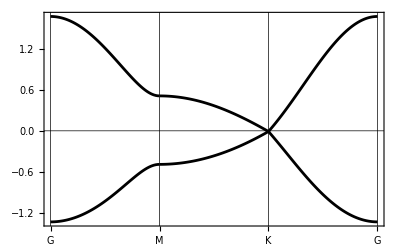

```mathematica
bandplot[
  graphenePath,
  60,
  grapheneHamiltonian,
  {e1 -> 0.05, r1 -> 0.02, t1 -> 0.5}
]
```

图中两条能带在 K 点相交。plotRange 只改变显示的能量范围，不会改变能量本征值或交叉位置。

考虑多个轨道和多个 Wyckoff 点

考虑多个轨道和多个 Wyckoff 点时，在 wyckoffposition 中逐个列出代表位置，再按相同顺序填写 basisFunctions。下面的 CsCl 模型在顶角位置放置 s 轨道，在体心位置放置 px、py、pz 轨道。完整 Hamiltonian 的行列顺序为 {s,px,py,pz}，包含 onsite 项和两个位置之间的跃迁。

```mathematica
csclOperations = msgop[gray[221]];
init[
  lattice -> {
    {a, 0, 0},
    {0, a, 0},
    {0, 0, a}
  },
  lattpar -> {a -> 1},
  wyckoffposition -> {
    {{0, 0, 0}, {0, 0, 0}},
    {{1/2, 1/2, 1/2}, {0, 0, 0}}
  },
  symminformation -> csclOperations,
  basisFunctions -> {{"s"}, {"px", "py", "pz"}}
];
csclHamiltonian = Sum[symham[i], {i, 2}];
validationBandPath = {
  {{{0, 0, 0}, {1/2, 0, 0}}, {"G", "X"}},
  {{{1/2, 0, 0}, {1/2, 1/2, 0}}, {"X", "M"}},
  {{{1/2, 1/2, 0}, {0, 0, 0}}, {"M", "G"}}
};
```

```mathematica
orbitalTable[]
```

Hamiltonian dimension = 4; representation mode = DirectProduct |  |  |  |  |  |  |  |  |  |  | 
H index | Site | Wyckoff orbit | Atom | Fractional position | Cartesian position | Local orbital | Input basis | Actual basis state | Spin structure | Spin state | Transport operation
1 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 1 | s | 1 | Spinless | None | None
2 | 2 | 2 | 1 | {1/2,1/2,1/2} | {1/2,1/2,1/2} | 1 | px | x | Spinless | None | None
3 | 2 | 2 | 1 | {1/2,1/2,1/2} | {1/2,1/2,1/2} | 2 | py | y | Spinless | None | None
4 | 2 | 2 | 1 | {1/2,1/2,1/2} | {1/2,1/2,1/2} | 3 | pz | z | Spinless | None | None

```mathematica
csclHamiltonian = FullSimplify[ExpToTrig[csclHamiltonian]];
MatrixForm[csclHamiltonian]
```

(e1 | -8 ⅈ t1 Cos[ky/2] Cos[kz/2] Sin[kx/2] | -8 ⅈ t1 Cos[kx/2] Cos[kz/2] Sin[ky/2] | -8 ⅈ t1 Cos[kx/2] Cos[ky/2] Sin[kz/2]
8 ⅈ t1 Cos[ky/2] Cos[kz/2] Sin[kx/2] | e2 | 0 | 0
8 ⅈ t1 Cos[kx/2] Cos[kz/2] Sin[ky/2] | 0 | e2 | 0
8 ⅈ t1 Cos[kx/2] Cos[ky/2] Sin[kz/2] | 0 | 0 | e2)

```mathematica
bandManipulate[validationBandPath, 30, csclHamiltonian]
```

含自旋的反幺正模型

自旋空间群可以分别指定空间操作和自旋旋转。下面的例子包含纯自旋 C4 旋转，以及半平移与时间反演的组合。在字典中，spin -> {S,0} 表示幺正操作，spin -> {S,1} 表示反幺正操作，其中 S 是自旋旋转矩阵。

```mathematica
identity3 = IdentityMatrix[3];
c4z = {{0, -1, 0}, {1, 0, 0}, {0, 0, 1}};
collinearSSG = <|
  "C4spin" -> <|
    "space" -> {identity3, {0, 0, 0}},
    "spin" -> {c4z, 0}
  |>,
  "tauHalfT" -> <|
    "space" -> {identity3, {1/2, 0, 0}},
    "spin" -> {identity3, 1}
  |>
|>;
init[
  lattice -> {{a, 0, 0}, {0, a, 0}, {0, 0, a}},
  lattpar -> {a -> 1},
  wyckoffposition -> {{{0, 0, 0}, {0, 0, 1}}},
  symminformation -> collinearSSG,
  basisFunctions -> {{"sup", "sdn"}},
  GenerateSymmetryGroup -> True
];
collinearHamiltonian = Sum[symham[i], {i, 2}];
validationBandPath = {
  {{{0, 0, 0}, {1/2, 0, 0}}, {"G", "X"}},
  {{{1/2, 0, 0}, {1/2, 1/2, 0}}, {"X", "M"}},
  {{{1/2, 1/2, 0}, {0, 0, 0}}, {"M", "G"}}
};
```

同样可以用 atompos 查看这两个原子的坐标和磁化方向：

```mathematica
atompos
```

{{{{0,0,0},{0,0,1}},{{1/2,0,0},{0,0,-1}}}}

位于 {0,0,0} 和 {1/2,0,0} 的两个原子分别沿 +z 和 -z 方向磁化。使用 showCrystalStructure 就可以画出原子及方向相反的磁矩：

```mathematica
showCrystalStructure[]
```

-Graphics3D-

```mathematica
MatrixForm[collinearHamiltonian]
```

(e2 | 0 | ⅇ^(-(ⅈ kx)/2) (t1+ⅈ t3)+ⅇ^((ⅈ kx)/2) (t2+ⅈ t4) | 0
0 | e1 | 0 | ⅇ^((ⅈ kx)/2) (t1+ⅈ t3)+ⅇ^(-(ⅈ kx)/2) (t2+ⅈ t4)
ⅇ^((ⅈ kx)/2) (t1-ⅈ t3)+ⅇ^(-(ⅈ kx)/2) (t2-ⅈ t4) | 0 | e1 | 0
0 | ⅇ^(-(ⅈ kx)/2) (t1-ⅈ t3)+ⅇ^((ⅈ kx)/2) (t2-ⅈ t4) | 0 | e2)

```mathematica
showSymmetryRepresentations[]
```

Representation mode: DirectProduct; dimension = 4; showing 3 of 8 operations |  |  |  |  |  |  | 
Index | Label | Generator | R | t | SpinAction | Type | Matrix
2 | GeneratedSSG2 | Yes | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | {0,0,0} | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1) | Unitary | (-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)
3 | C4spin | Yes | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | {0,0,0} | (0 | -1 | 0
1 | 0 | 0
0 | 0 | 1) | Unitary | ((1-ⅈ)/(√2) | 0 | 0 | 0
0 | (1+ⅈ)/(√2) | 0 | 0
0 | 0 | (1-ⅈ)/(√2) | 0
0 | 0 | 0 | (1+ⅈ)/(√2))
5 | GeneratedSSG5 | Yes | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | {1/2,0,0} | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1) | Antiunitary | (0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)

```mathematica
bandManipulate[validationBandPath, 30, collinearHamiltonian]
```

DirectProduct 使用各位置所给轨道的对称变换，Induced 则从代表位置的局域态出发，生成对称相关的态。例如，立方晶系的 p 轨道模型用 DirectProduct 时需要给出 px、py、pz，而用 Induced 时可以从代表位置的 px 出发。连接两个位置的操作也可以含有时间反演。

相关函数与教程

init ▪ symham ▪ orbitalTable ▪ showbonds ▪ bandManipulate ▪ General Examples

历史